# 神经网络练习

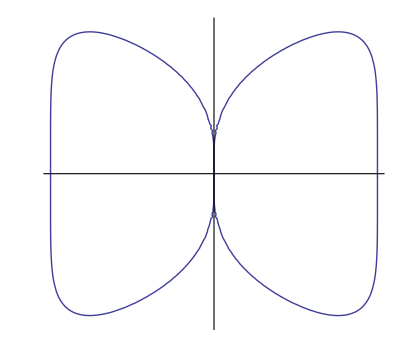

```mathematica
Entity["PlaneCurve","ButterflyCurve1"][EntityProperty["PlaneCurve","Graphics"]]
```

### 交叉熵损失

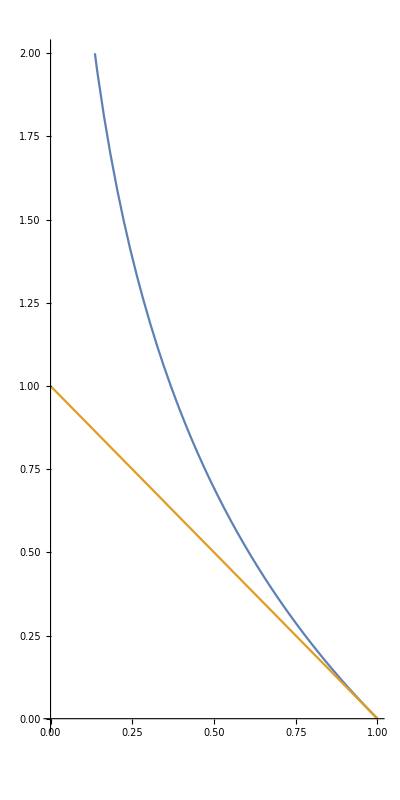

```mathematica
Plot[{-Log[x],1-x},{x,0,1},PlotRange->{{0,1},{0,2}},AspectRatio->2]
```

```mathematica
net=NetChain[{5,Tanh,1},"Input"->1]
```

NetChain[<>]

```mathematica
inet=NetInitialize[net,Method->{"Random","Biases"->2}]
```

NetChain[<>]

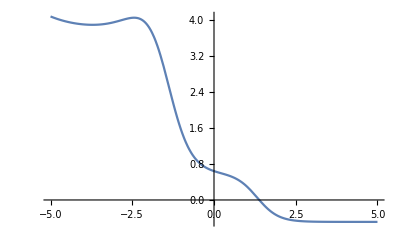

```mathematica
Plot[inet[x],{x,-5,5}]
```

```mathematica
Plot[inet[x],{x,-5,5}]
```

-Graphics-

```mathematica
img=Import["C:\\Users\\HuiLing\\Desktop\\sudoku_001.png"]
```

-Graphics-

```mathematica
Binarize[img]
```

-Graphics-

```mathematica
ColorNegate[%41]
```

-Graphics-

```mathematica
EdgeDetect[ColorNegate@Binarize@img]
EdgeDetect[img]
```

-Graphics-

-Graphics-

```mathematica
EdgeDetect[ColorNegate@Binarize@img,6,0.1,Method->{"Canny","StraightEdges"->0.1}]
```

-Graphics-

```mathematica
contours=ImageMeasurements[ColorNegate@Binarize@img,"Contours"]
```

{Line[{{0,900},{0,841},{1200,841},{1200,900},{0,900}}],236,Line[{{1013,43},{1013,41},{1024,41},{1024,43},{1013,43}}]}
 |  |  |  |

找出点数最多的Line，（但并不是想要的结果）

```mathematica
l=MaximalBy[contours,Length[#[[1]]]&];
Length[l[[1,1]]]
```

215

找出围成区域面积最大的Line，

```mathematica
s=MaximalBy[contours,Area[Region@Polygon[#[[1]]]]&];
Polygon[s[[1,1]]]
Region
```

Polygon[…]

Region

```mathematica
Polygon[…]
```

```mathematica
Area[Polygon@contours[[76,1]]]
```

403860

```mathematica
Polygon@contours[[70,1]]
```

Polygon[…]

```mathematica
Manipulate[HighlightImage[img,contours[[i]]],{i,1,Length@contours,1}]
```

```mathematica
面积
```